# PHAS2443: Practical Mathematics II Exercises 1: Programming Styles Model Solutions

This set of exercises starts with a few simple revision problems, before setting up a module for an alternative method of finding the zero of a function (Newton's method was discussed in the lecture). Remember how useful the help file can be.

1. Given a list, {a,b,c,d,e,f,g,h,i,j,k}, form a new list containing just the elements in the even-numbered positions (2,4,6,...). Do this in three ways:
                  a) with a Do loop and AppendTo
                  b) with a Table command
                  c) using Partition and taking part of the transpose of the r esult.
       By enclosing your schemes in a Do loop and repeating them 100000 times, compare the timings.

```mathematica
ll={a,b,c,d,e,f,g,h,i,j,k};
nl={}

(*---------- N.B. It is good practice to use an integer 'counter' with a different name from any other variables, list elements, etc. ----------*)
Do[AppendTo[nl,ll[[icount]] ],{icount,2,Length[ll],2}]  
nl
nl=Table[ll[[icount]],{icount,2,Length[ll],2}]
nl=Transpose[Partition[ll,2]][[2]]
```

{}

{b,d,f,h,j}

{b,d,f,h,j}

{b,d,f,h,j}

```mathematica
Timing[Do[nl={};
Do[AppendTo[nl,ll[[icount]] ],{icount,2,Length[ll],2}],{icount,1,100000}]]
Timing[Do[nl=Table[ll[[icount]],{icount,2,Length[ll],2}],{icount,1,100000}]]
Timing[Do[nl=Transpose[Partition[ll,2]][[2]],{icount,1,100000}]]
```

{1.08595,Null}

{0.608629,Null}

{0.731234,Null}

Comments:

Note that to time a function which takes a very short time to run the appropriate technique is
  Timing[Do[thing[],{lotsoftimes}]]
and not, for example
 Plus@@Table[Timing[thing][[1]],{lotsoftimes}].
      The reason for this is that the clock that is used by Timing[] only 'ticks' every $TimeUnit seconds (typically 1/1000 seconds). This means that there is a good chance that the clock will not 'tick' while the operation is carried out, and the time returned for a single call of the function will be zero. The first version times many executions of the function, and only looks at the clock at the start of the first and the end of the lotsoftimesth -- this works.
    
     There is a further potential problem with the AppendTo timing. If you time using
     nl={}
     Timing[Do[Do[AppendTo[nl,ll[[i]] ],{i,2,Length[ll],2}],{i,1,100000}]]
    then the big Do loop will keep appending items to nl. This means on the nth run through the loop items are being appended to a list that is 5n long, and the overhead of managing the allocation of a new list that long and throwing away the old list becomes very large. Actually this shows that AppendTo is rather an inefficient function. If we use
    Timing[Do[nl={};
    Do[AppendTo[nl,ll[[i]] ],{i,2,Length[ll],2}],{i,1,100000}]]
    then every run through the outer Do loop is handling a list of the same length.
     If we do want to accumulate a lot of results, a more efficient procedure uses the Sow, Reap pair. This is more efficient because it does not have the overhead of list management: in this case a single item is Sown to memory at each pass through the inner Do loop, and one pass through the Sown items with Reap accumulates the required list. Here is an example of this method, showing that it gives the same result as AppendTo.

```mathematica
nl1={};
Timing[Do[Do[AppendTo[nl1,ll[[ii]] ],{ii,2,Length[ll],2}],{ii,1,1000}]]
Length[nl1]
nl2={};
Timing[nl2=Reap[Do[Do[Sow[ll[[ii]] ],{ii,2,Length[ll],2}],{ii,1,1000}]][[2,1]];]
Length[nl2]
nl1==nl2
```

{0.142433,Null}

5000

{0.00852,Null}

5000

True

2. Create a function abwordq that accepts as an argument a string containing a word, and returns True if the letters in the word are in alphabetical order, False if they are not. Thus abwordq["how"] will return True, but abwordq["why"] will return False.

Then use the following code to read in a dictionary:
wordfile=DictionaryLookup[x__];
and find the words in that dictionary that have their letters in alphabetical order.

  Repeat, this time looking for palindromes (words that read the same forwards as backwards).

```mathematica
abwordq[w_String]:=OrderedQ[Characters[w]]
abwordq["how"]
abwordq["why"]
```

True

False

```mathematica
wordfile=DictionaryLookup[x__];
Length[wordfile]
Select[wordfile,abwordq]
```

92518

{a,aah,abbe,abbé,abbes,abbés,abbess,abbey,abbot,Abbott,Abby,ABC,Abe,Abel,abet,abhor,abhors,ably,abort,abs,ABS,abuzz,AC,accent,accept,access,accost,ace,aces,achoo,achy,Acrux,act,ad,AD,add,adder,adders,adds,Aden,adept,adios,adiós,ado,adopt,ads,adz,aegis,affix,afoot,aft,aglow,ago,ah,ahoy,ail,ails,aim,aims,Ainu,air,airs,airy,all,allot,allow,alloy,ally,almost,alms,alp,alps,Alps,am,AM,ammo,Amos,amp,amps,Amy,an,Ann,annoy,ans,ant,any,apt,art,Art,arty,as,ass,at,ax,BBC,BC,be,bee,beef,beefs,beefy,been,beep,beeps,beer,beers,beery,bees,beet,befit,beg,begin,Begin,begins,begot,begs,bell,Bell,bellow,Bellow,bells,belly,below,belt,Ben,Benny,bent,Benz,berry,Berry,Bert,Bess,best,Best,bet,Betty,bevvy,bevy,bey,bi,bijou,bijoux,Biko,bill,Bill,billow,billowy,bills,billy,Billy,bin,bins,biopsy,bios,BIOS,bis,bit,bitty,biz,bloop,bloops,blot,blow,blowy,BMW,boo,boor,boors,boos,boost,boot,booty,bop,bops,Boru,boss,bossy,bow,box,boxy,boy,brr,buy,buzz,by,CD,cell,cello,cellos,cells,Celt,cent,CEO,chi,Chi,chill,chills,chilly,chimp,chimps,Chimu,chin,chino,chinos,chins,chintz,chip,chippy,chips,chis,chit,chivvy,chivy,choosy,chop,choppy,chops,Chou,chow,cissy,city,clop,clops,clot,cloy,CNN,coo,coop,coops,Coors,coos,coot,cop,cops,copy,Cory,cost,cot,cow,cox,Cox,coy,Coy,CPU,crux,Crux,Cruz,cry,cs,cw,DDT,Dee,deem,deems,deep,deeps,deer,deers,deft,defy,Deimos,deist,deity,Deity,dell,dells,demo,demos,den,Denny,dens,dent,deny,Derry,derv,dew,dewy,dhow,dill,dills,dilly,dim,dims,din,Dino,dins,dint,Dior,dip,dippy,dips,dirt,dirty,dis,ditty,ditz,divvy,Dix,DJ,do,door,doors,dory,dos,DOS,doss,dost,dot,Dot,dotty,Dow,dry,eek,eeks,eel,eels,eff,effort,effs,egg,Eggo,eggs,ego,egos,eh,ell,ells,elm,Elmo,elms,Eloy,Ely,em,Emmy,Emory,empty,ems,emu,en,Enos,ens,envy,er,err,errs,erst,es,ET,ex,fill,fills,filly,film,films,filmy,filo,fin,Finn,Finns,finny,fins,fir,firs,first,fist,fit,fix,fizz,Flo,floor,floors,flop,floppy,flops,Flory,floss,flossy,flow,flu,flux,fly,FM,foot,footy,fop,fops,for,fort,forty,fox,Fox,foxy,fry,Fry,fuzz,ghost,GI,Gil,gill,Gill,gills,gilt,gimp,gimps,gimpy,gin,Ginny,Gino,gins,Ginsu,girt,gist,git,glop,gloppy,glops,glory,gloss,glossy,glow,GMT,GNP,gnu,go,goo,goop,GOP,gory,gos,got,GP,gs,guv,guy,Guy,hi,hill,Hill,hills,hilly,hilt,him,hims,hint,hip,hips,his,hiss,Hiss,hit,HIV,hm,HMO,ho,hoop,hoops,hoot,hop,hops,host,Host,hot,how,HQ,I,ill,ills,imp,imps,in,inn,inns,ins,IOU,IQ,IRS,is,it,IT,ivy,Ivy,Jo,jot,joy,Joy,knot,knotty,know,Knox,KO,Kory,ks,kw,kW,lo,loo,loop,loops,loopy,loos,loot,lop,lops,lorry,loss,lost,lot,Lot,Lott,Lou,low,lox,ls,luv,Luz,moo,moor,Moor,moors,Moors,moos,moot,mop,mops,Mort,moss,Moss,mossy,most,mot,Mott,mow,Mr,Mrs,ms,Ms,mu,my,no,nor,nosy,not,now,nu,oops,ops,opt,or,Orr,ow,ox,Oz,pry,psst,rs,Rx,Stu,sty,tux,TV,Ty,WWW}

```mathematica
palinq[w_String]:=Characters[w]==Reverse[Characters[w]]
Select[wordfile,palinq]
```

{a,aha,aka,bib,bob,boob,bub,CFC,civic,dad,deed,deified,did,dud,DVD,eke,ere,eve,ewe,eye,gag,gig,huh,I,kayak,kook,level,ma'am,madam,mam,MGM,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,poop,pop,pup,radar,redder,refer,repaper,reviver,rotor,sagas,sees,seres,sexes,shahs,sis,solos,SOS,stats,stets,tat,tenet,TNT,toot,tot,tut,wow,WWW}

Comments

This is a good time to remind you of the concept of overloading functions. What this means is that the same function name can be used several times, and different actions attributed to it depending on the pattern that is matched by the argument(s) when the function is called: you could think of the function that remembers its previous values, as described in the first lecture, as an example of dynamic overloading. This is all very useful -- but it can also shoot you in the foot when you are developing a function. You had a first stab at a definition, then rewrote it with a different argument pattern -- but Mathematica did not throw away your first attempt, it tried to slot it in to its logical sequence of function definitions ordered from most specific argument pattern to least specific. This means that it is a good idea to put at the beginning of your block of functions defining fun the statement Remove[fun] to make sure you start with a clean slate, with those previous attempts deleted.

Another important point is that Mathematica treats some things as atomic, that is, fundamental and not normally to be split. Some of these are reasonably obvious: symbols and integers, for example. The function AtomQ tells us whether something is an atom:

```mathematica
Map[AtomQ,{x,1,1+3I,2/3,15x+7}]
```

{True,True,True,True,False}

You might be slightly surprised to see that a rational such as 2/3 is regarded as atomic, as is a complex number, but this is related to the fact that Mathematica likes to do exact arithmetic when it can. There are some other structures which are patently far from atomic, but are treated as such by Mathematica: for example, there is a special structure for storing sparse arrays, that is, arrays which have a large fraction of zeros. If we give Mathematica such a matrix and as for it to be converted to sparse form, the result is atomic.

```mathematica
MatrixForm[mm={{1,0,0},{0,0,0},{0,0,0}}]
mms=SparseArray[mm]
AtomQ[mms]
```

(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

SparseArray[<1>, {3, 3}]

True

In a sense, what Mathematica is saying here is 'I have an object which I know how to deal with, but the details are too messy for you to bother with'.

  OK, back to this question. A string is atomic,

```mathematica
AtomQ["any old string"]
```

True

and this means that a very intelligent attempt to create a pattern which says 'look for a string containing any number of elements' by using "a___" will not work: "a___" is a string, and represents exactly those characters within the quotes, without any additional Mathematica syntactical interpretation.

  All is not lost, though, as whilst Mathematica defines its own periodic table of atoms, it also provides atomsplitters: for example,
      Integers can be split into IntegerDigits
      Strings can be split into Characters
      Complexes can be split into Re and Im parts.
    So for these word-manipulation examples the appropriate pattern is a_ or a_String, and we can use Characters to break a down.

3. Convert the following function to one that does not have conditional parts (/;), but uses pattern matching in the argument list instead.
        f[x_,y_]:=x-y/;IntegerQ[x]
    f[x_,y_]:=x[[1]]+y/;Head[x]==List&&IntegerQ[First[x]].

```mathematica
f[x_Integer,y_]:=x-y
f[{x_Integer,___},y_]:=x+y
```

(Note that it is perfectly correct syntax to have three underscores without a symbol. It is the underscores that denote the pattern, and if we are not going to use that particular pattern, we need not name it. Of course,    
    f[{x_Integer,z___},y_]:=x+y 
would be just as correct.)

An alternative approach for the second case is to set up a function which returns True or False and use that

```mathematica
Remove[f]
ft[x_]:=IntegerQ[x[[1]]]
f[x_List?ft,y_]:=x[[1]]+y
f[1,2]
f[{1,2},3]
f[{1.1,2},3]
```

f[1,2]

4

f[{1.1,2},3]

and one can do the same using a pure function

```mathematica
Remove[f]
f[x_List?(IntegerQ[#[[1]]]&),y_]:=x[[1]]+y
f[1,2]
f[{1,2},3]
f[{1.1,2},3]
Remove[f]
f[x_List?(Function[x,IntegerQ[x[[1]]]]),y_]:=x[[1]]+y
f[1,2]
f[{1,2},3]
f[{1.1,2},3]
```

f[1,2]

4

f[{1.1,2},3]

f[1,2]

4

f[{1.1,2},3]

but the following will not work as the symbol x in the expression after the question mark is not equated to the result of the pattern matched by x_List.

```mathematica
Remove[f]
f[x_List?IntegerQ[x[[1]]],y_]:=x[[1]]+y
f[1,2]
f[{1,2},3]
f[{1.1,2},3]
```

Part::partd: Part specification x ⟦ 1 ⟧ is longer than depth of object.

f[1,2]

f[{1,2},3]

f[{1.1,2},3]

4. The secant method is a method for finding the zero of a function without using derivatives. It starts with two x values, x0 and x1, say, evaluates the value of the function at those points, draws a straight line through the points and finds where it intersects the axis, x2, and then repeats starting with x1 and x2.
  Here is an illustration of the first step of the method.

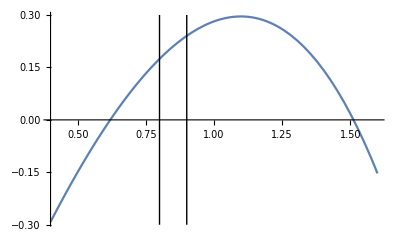

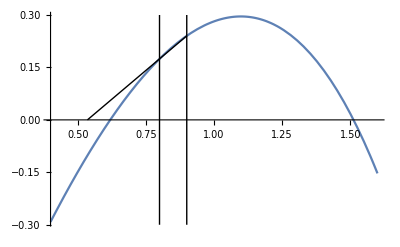

```mathematica
fn:=3 x-ⅇ^x;
p1=Plot[fn,{x,0.4,1.6}];
x0=x->0.8;x1=x->0.9;
l1=Graphics[Line[{{x,-0.3},{x,0.3}}/.x0]];
l2=Graphics[Line[{{x,-0.3},{x,0.3}}/.x1]];
l3=Graphics[Line[{{x,fn}/.x1,{(x/.x0)-((fn/.x0) ((x/.x1)-(x/.x0)))/((fn/.x1)-(fn/.x0)),0}}]];
Show[p1,l1,l2]
Show[p1,l1,l2,l3]
```

Write a module to implement the secant method, using a procedural approach. Your function should return the sequence of x values used.
  Modify your function to use a functional approach.
  Check each version by looking for the roots of 3x - Exp[x].

```mathematica
secant[f_,x_,x0_,x1_,eps_:10^-10,max_:100]:=Module[{xw0=x0,xw1=x1,f0=N[f/.x->x0],f1,xw,its={x0,x1}},Do[f1=N[f/.x->xw1];If[Abs[f1]<eps,Break[]];xw=xw1-f1(xw1-xw0)/(f1-f0);its={its,xw};{xw0,xw1,f0}={xw1,xw,f1},{max}];Flatten[its]]
secant[3x-Exp[x],x,0.8,0.9]
3x-Exp[x]/.x->%[[-1]]
```

{0.8,0.9,0.535419,0.643958,0.620648,0.619028,0.619061,0.619061}

1.31317×10^-12

Here we build up a list of {x0,x1,f0,f1}.

```mathematica
secant2[f_,x_,x0_,x1_,eps_:10^-10,max_:100]:=Module[{tt},tt=Transpose[NestWhileList[{#[[2]],x,#[[4]],f}/.(x->#[[2]]-#[[4]](#[[2]]-#[[1]])/(#[[4]]-#[[3]]))&,{x0,x1,f/.x->x0,f/.x->x1},Abs[#[[4]]]>eps&,1,max]];
Append[tt[[1]],tt[[2,-1]]]]
secant2[3x-Exp[x],x,0.8,0.9]
3x-Exp[x]/.x->%[[-1]]
```

{0.8,0.9,0.535419,0.643958,0.620648,0.619028,0.619061,0.619061}

1.31317×10^-12

A.H. Harker
Physics and Astronomy, UCL
January 2008, revised January 2009.
Minor revision, Jan 2015, Jan2016 N.A.